## Section | Quantum coherence and correlation functions

### Classical coherence functions

Consider the classic Young’s two slit experiment setup

The electric field on the detector at time t can be written as the superposition of the fields incoming from the slits at times t_1=t-s_1/c and t_2=t-s_2/c. The constants K_1,K_2 are geometric factors.

Optical light detectors have a long response time so what is measured effectively is the average intensity

The time average of a function f(t) is defined as:

Defining a time expectation function:

```mathematica
TimeExpectation[f_]:=Limit[Integrate[f,{t,0,T}]/T,T->∞]
```

For example, for the function (Sin(t))^2 we get the expected result of 1/2:

```mathematica
TimeExpectation[Sin[t]^2]
```

1/2

Or a general cosine function:

```mathematica
Simplify[TimeExpectation[Cos[t m x ]^2],Element[{m,x,a},Reals]]
```

1/2

The intensity can be expressed as:

the first two terms are related to intensities from each slit (I_1, I_2), and the last term is the interference term

Let x_i=r_i,t_i, the first order normalized coherence function can be defined as:

The intensity at the screen can be rewritten in terms of the coherence function, using the polar form of the complex numbers K_1,K_2 and defining θ=ψ_1-ψ_2 the phase difference related to path length difference

When |γ^(1)(x_1,x_2)|=1 there is complete coherence, |γ^(1)(x_1,x_2)|=0 means there is no coherence at all, intermediate values are related to partial coherence

Fringe visibility is defined as:

So we can express the visibility  in terms of the first order coherence function:

```mathematica
With[{Imax = Subscript[I, 1]+Subscript[I, 2]+√(2 Subscript[I, 1] Subscript[I, 2]) Abs[γ1],Imin= Subscript[I, 1]+Subscript[I, 2]-√(2 Subscript[I, 1] Subscript[I, 2]) Abs[γ1]},(Imax-Imin)/(Imax+Imin)]//Simplify
```

(√2 √(I_1 I_2) Abs[γ1])/(I_1+I_2)

when , the maximum value of the visibility is , and clearly the minimum is zero where there is complete incoherence

Consider monochromatic light propagating in the z direction:

```mathematica
Efield[z_,t_]:=E0 ⅇ^(ⅈ(k z - ω t))
```

Electric field at times t and t+τ:

```mathematica
{Efield[z,t],Efield[z,t+τ]}
```

{ⅇ^(ⅈ (k z-t ω)) E0,ⅇ^(ⅈ (k z-(t+τ) ω)) E0}

Calculate ⟨E*(z,t)E(z,t+τ)⟩, at position z and times t and t+τ:

```mathematica
TimeExpectation[ComplexExpand@Conjugate@Efield[z,t]Efield[z,t+τ]]
```

ⅇ^(-ⅈ τ ω) E0^2

### Quantum approach to coherence functions

Analogously to the classical γ^(1), the normalized first-order coherence function is:

where 0<=|g^(1)|<=1 determines if it is coherent, partial coherence or incoherent

### Higher-order coherence functions

If the position has a fixed value, g^(2) depends only on the time difference τ

For single-mode states the second-order coherence assumes a simple form

and does not depend on τ, so g^2(τ)=g^2(0) which can be easier to calculate

For a Fock state n>=1, the g_2(0) has the value of  1-1/n:

```mathematica
FindSequenceFunction[Array[G2Coherence@*FockState,$FockSize-1,1]][n]//Apart
```

1-1/n

For the vacuum state g^(2) is not defined from the mathematical definition, we can also see that plugging n=0 in the above formula. However, the value that makes sense from a experimental point of view is just 0, there cannot be coherence with a 0 photon state

```mathematica
G2Coherence[FockState[0]]//Quiet
```

Indeterminate

Evidently, the superposition 1/(√2)(|0⟩ + |1⟩) has zero g^(2):

```mathematica
G2Coherence[QuantumState["+",$FockSize]]
```

0

Also for the mixed state of the number states 0 and 1:

```mathematica
1/2Total@Array[FockState[#]["MatrixState"]&,2,0]
```

1/2 00+1/2 11

```mathematica
G2Coherence[%]
```

0

For a coherent state  |α⟩, the value of g^(2)=1:

```mathematica
G2Coherence[CoherentState[][1.2]]
```

1.

Depending on the value of α and the truncation size used, we see numerical error can be relevant:

```mathematica
g2s = ParallelTable[G2Coherence[CoherentState[m][α]],{m,{12,16,24}},{α,0.1,4,0.1}];
```

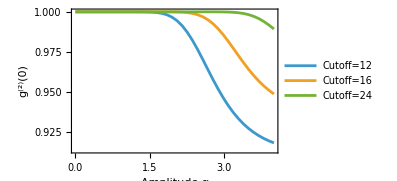

```mathematica
ListLinePlot[g2s,]
```

For a thermal state g^(2)=2:

```mathematica
G2Coherence[ThermalState[1.,30]]
```

2.

Summarizing the results, we can say:

g^(2)=1:  Poissonian statistics (coherent light)

g^(2)<1: Sub-Poissonian (antibunching, nonclassical light)

g^(2)>1: Super-Poissonian (bunching, thermal light)

g^(2)=0: Single-photon state

In general, the n-th order quantum correlation function is:

And the n-th order coherence function can be defined as:

Vocabulary

G2Coherence |   | Computes g^(2)(0)for a single mode quantum state
G1Correlation |   | XXXX

Exercises

1 + 2 + 3

References

Use Chicago Style in your reference section. We have provided this References section for those who prefer in chapter reference sections.  However, generally we preferences to be at the end of the book as a Bibliography.  For citations within chapters, please use standard (Author, Date) in-text citation.